### Basic:

```mathematica
SetOptions[ListPlot,BaseStyle->{FontSize->14},LabelStyle->{14,GrayLevel[0.2]}, ImageSize->300, Frame->True, PlotStyle->PointSize[0.02]];
```

```mathematica
FNJ=FileNameJoin;
```

```mathematica
RelativeDir[dir_]:=FileNameJoin[{NotebookDirectory[],dir}]
```

```mathematica
Replicate[list_,n_]:=Flatten[Transpose[ConstantArray[list,n]]]
```

```mathematica
ToText[list_]:=StringJoin[Riffle[ToString[#]&/@list,"\n"]]
```

```mathematica
ShiftLeft[list_,n_]:=Drop[PadLeft[list,Length[list]+n],-n]
```

```mathematica
Half[list_]:= Take[list, Floor[Length[list]/2]]
```

### Before simulation:

```mathematica
(*-------parameters-------*)
td = 3; blocks = 4; l = 100;
(*------------------------*)
(*data=RandomInteger[{-16,16},l];
ker = RandomInteger[{-16,16},td*blocks];
upKer = RandomInteger[{-16,16},td*6];*)
```

```mathematica
expected=ListConvolve[Reverse[ker],data,1,0];
```

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[ker].

ListConvolve::kldims: The kernel Reverse[ker] and list data are not both non-empty lists with the same tensor rank.

```mathematica
Max[Abs[expected]]
```

Abs[ListConvolve[Reverse[ker],data,1,0]]

```mathematica
(*Export[RelativeDir["data.dat"],ToText[Replicate[data,td]]];Export[RelativeDir["coefs.dat"],ToText[ker]];Export[RelativeDir["upsamp_coefs.dat"],ToText[upKer]];*)
```

### After simulation:

```mathematica
ker
```

ker

```mathematica
expected
```

ListConvolve[Reverse[ker],data,1,0]

```mathematica
upKer
```

upKer

```mathematica
Max[lol]
```

lol

```mathematica
upIn=Flatten@Riffle[expected,{ConstantArray[0,2]}]
```

Riffle::list: List expected at position 1 in Riffle[ListConvolve[Reverse[ker],data,1,0],{{0,0}}].

Riffle[ListConvolve[Reverse[ker],data,1,0],{{0,0}}]

```mathematica
lol=ListConvolve[Reverse[upKer],upIn,1,0]
```

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[upKer].

ListConvolve::kldims: The kernel Reverse[upKer] and list Riffle[ListConvolve[Reverse[ker],data,1,0],{{0,0}}] are not both non-empty lists with the same tensor rank.

ListConvolve[Reverse[upKer],Riffle[ListConvolve[Reverse[ker],data,1,0],{{0,0}}],1,0]

```mathematica
2^13
```

8192

```mathematica
Floor[lol/2^8]
```

Riffle::list: List expected at position 1 in Riffle[ListConvolve[Reverse[ker],data,1,0],{{0,0}}].

ListConvolve::kldims: The kernel Reverse[upKer] and list Riffle[ListConvolve[Reverse[ker],data,1,0],{{0,0}}] are not both non-empty lists with the same tensor rank.

Floor[1/256 ListConvolve[Reverse[upKer],Riffle[ListConvolve[Reverse[ker],data,1,0],{{0,0}}],1,0]]

```mathematica
result
```

result

```mathematica
result=Flatten[Import[RelativeDir[FNJ[{"edit_firIP_v1_0.sim","sim_1","behav","xsim","out.dat"}]]]];
```

```mathematica
LongestCommonSubsequence[result,lol]
```

LongestCommonSubsequence[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,2,2,1,0,3,2,-2,0,0,-4,-6,-4,-1,-6,-4,8,6,4,1,7,4,-7,-2,-2,-3,-5,-4,6,4,2,-1,3,2,2,5,4,-8,-5,-4,2,-2,-1,1,1,0,-4,-4,-3,5,4,3,-9,-7,-5,4,-1,-1,2,3,2,-1,1,1,-8,-9,-6,12,8,6,-14,-11,-8,8,2,1,-4,-4,-3,1,-1,-1,9,12,8,-16,-10,-7,7,1,1,-4,-4,-3,5,4,2,-6,-4,-3,4,2,2,-9,-9,-6,1,-6,-4,9,8,5,-1,5,4,-8,-5,-4,-4,-8,-6,6,1,1,0,2,1,1,4,2,0,3,2,-8,-8,-5,2,-3,-2,4,3,2,2,6,4,-6,-2,-2,-5,-8,-6,8,4,2,-7,-6,-4,2,-2,-1,6,8,5,-10,-6,-4,6,3,2,-3,0,0,-1,-2,-1,-1,-2,-2,1,0,0,-6,-7,-5,10,8,5,-3,3,2,-6,-5,-4,6,4,3,-8,-6,-4,9,8,5,-4,2,1,-7,-8,-5,-1,-7,-5,8,5,4,-6,-3,-2,-2,-5,-4,7,5,3,0,5,3,-9,-7,-5,10,8,5,-13,-9,-6,8,3,2,1,5,3,-7,-4,-3,2,0,0,3,5,3,-11,-10,-7,1,-7,-5,10,8,6,-7,-2,-1,5,6,4,-12,-10,-7,4,-2,-2,3,3,2,3,7,5,-4,2,1,1,3,2,-7,-6,-4,6,4,2,-6,-4,-3,6,5,3,2,7,5,-14,-12,-8,4,-4,-3,5,3,2,-1,2,1,0,2,2,-2,0,0,-6,-7,-5,6,2,1,1,4,3,-6,-3,-2,1,0,0,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},ListConvolve[Reverse[upKer],Riffle[ListConvolve[Reverse[ker],data,1,0],{{0,0}}],1,0]]

### Random:

```mathematica
2224189. /2^16
```

33.9384

### Samples from fpga:

```mathematica
fker = Flatten@Import[RelativeDir["coefs.dat"]]
```

{4563,-5780,100032,-103434,12,-15,250,43032,15003,-79934,25666,76498}

```mathematica
fupker =  Flatten@Import[RelativeDir["upsamp_coefs.dat"]]
```

{-10009,10343,15133,11501,-111,5}

```mathematica
datain=Downsample[Flatten@Import[RelativeDir["data.dat"]],3]
```

{10,8,8,-15,-14,7,8,9,8,15,10,-3,-12,12,-16,13,1,-4,2,-15,2,-14,3,-6,-3,-14,8,11,-3,3,1,0,-7,-4,-9,-16,14,13,-2,-10,-12,1,-1,14,14,-2,7,-2,-10,-12,2,-9,9,4,2,7,-16,2,-9,-8,2,16,16,6,-3,0,0,8,-15,9,3,-15,-14,7,5,5,10,-3,10,-14,-2,13,7,-14,-5,-6,9,-8,-1,5,-1,12,15,16,9,-3,-4,14,6,-8}

```mathematica
Floor[ListConvolve[Reverse[fker],datain,1,0]/2^12]
```

{186,212,4,-350,-378,449,496,-127,-326,298,221,412,-314,-87,77,-224,344,-443,-15,257,133,-572,605,-720,144,-210,-7,889,-651,130,-218,299,-261,208,-593,-369,566,411,-318,-554,124,199,304,268,-491,-191,216,444,-120,-549,278,-372,-86,558,-356,243,6,-81,-129,52,-461,588,260,-301,325,-358,556,163,-493,-437,409,-190,-321,376,398,-427,572,-605,218,371,-233,15,352,-655,-422,610,-84,472,-629,-134,224,537,171,264,-373,293,-242,367,502,-767}

```mathematica
Floor[764980/2^12]
```

186

```mathematica
Floor[ListConvolve[Reverse[fupker], Flatten[Riffle[Floor[ListConvolve[Reverse[fker],datain]/2^12],{{0,0}}]]]/2^20]
```

{-8,-5,-4,2,-2,-1,1,1,0,-4,-4,-3,5,4,3,-9,-7,-5,4,-1,-1,2,3,2,-1,1,1,-8,-9,-6,12,8,6,-14,-11,-8,8,2,1,-4,-4,-3,1,-1,-1,9,12,8,-16,-10,-7,7,1,1,-4,-4,-3,5,4,2,-6,-4,-3,4,2,2,-9,-9,-6,1,-6,-4,9,8,5,-1,5,4,-8,-5,-4,-4,-8,-6,6,1,1,0,2,1,1,4,2,0,3,2,-8,-8,-5,2,-3,-2,4,3,2,2,6,4,-6,-2,-2,-5,-8,-6,8,4,2,-7,-6,-4,2,-2,-1,6,8,5,-10,-6,-4,6,3,2,-3,0,0,-1,-2,-1,-1,-2,-2,1,0,0,-6,-7,-5,10,8,5,-3,3,2,-6,-5,-4,6,4,3,-8,-6,-4,9,8,5,-4,2,1,-7,-8,-5,-1,-7,-5,8,5,4,-6,-3,-2,-2,-5,-4,7,5,3,0,5,3,-9,-7,-5,10,8,5,-13,-9,-6,8,3,2,1,5,3,-7,-4,-3,2,0,0,3,5,3,-11,-10,-7,1,-7,-5,10,8,6,-7,-2,-1,5,6,4,-12,-10,-7,4,-2,-2,3,3,2,3,7,5,-4,2,1,1,3,2,-7,-6,-4,6,4,2,-6,-4,-3,6,5,3,2,7}

```mathematica
2^14
```

16384

```mathematica
85*6229+960
```

530425

```mathematica
snaps=Reverse/@Import[RelativeDir["snap20.dat"]];
```

```mathematica
(*afirIn = snaps[[2]]*)
```

```mathematica
(*afirOut = snaps[[10]]*)
```

```mathematica
(*expafirOut=Floor[ListConvolve[fupker, Flatten[Riffle[Downsample[afirIn,3],{{0,0}}]]]/2^20]*)
```

```mathematica
(*LongestCommonSubsequence[afirOut,expafirOut]*)
```

```mathematica
snaps[[2]]
```

{-4350,-4118,-4022,-4308,-4300,-3796,-4202,-4350,-3486,-4022,-4308,-3121,-3796,-4202,-2666,-3486,-4022,-2165,-3121,-3796,-1690,-2666,-3486,-1190,-2165,-3121,-649,-1690,-2666,-124,-1190,-2165,417,-649,-1690,940,-124,-1190,1410,417,-649,1895,940,-124,2395,1410,417,2863,1895,940,3245,2395,1410,3559,2863,1895,3816,3245,2395,4021,3559,2863,4141,3816,3245,4177,4021,3559,4204,4141,3816,4100,4177,4021,3865,4204,4141,3490,4100,4177,2976,3865,4204,2295,3490,4100,1562,2976,3865,832,2295,3490,47,1562,2976,-739,832,2295,-1456,47}

```mathematica
firIn=Downsample[snaps[[2]],3,1]; firOut = Downsample[snaps[[3]],3,1]
```

{52252,45290,36679,26759,15945,4652,-6764,-17992,-28719,-38586,-47210,-54232,-59412,-62685,-64165,-64068,-62623,-60010,-56340,-51680,-46117,-39777,-32819,-25412,-17708,-9833,-1895,6014,13816,21444,28815,35808,42261,48004}

```mathematica
firOutExp=Floor[ListConvolve[fker,firIn]/2^12]
```

{-66701,-64621,-60478,-56623,-50884,-45843,-40783,-31077,-21243,-13544,-6203,1403,9430,19084,26836,32337,39743,45114,50066,52909,54263,54984,57305}

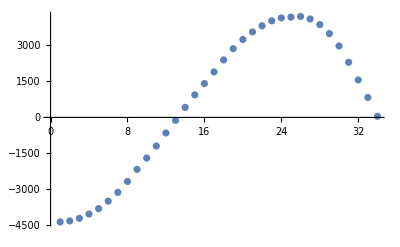

```mathematica
ListPlot[firIn]
```

```mathematica
firOut
```

{52252,45290,36679,26759,15945,4652,-6764,-17992,-28719,-38586,-47210,-54232,-59412,-62685,-64165,-64068,-62623,-60010,-56340,-51680,-46117,-39777,-32819,-25412,-17708,-9833,-1895,6014,13816,21444,28815,35808,42261,48004}

```mathematica
LongestCommonSubsequence[firOutExp,firOut]
```

{}

```mathematica
s
```

s

```mathematica
TableForm[Join[{Range[Length[snaps]]},Transpose@snaps]];
```

```mathematica
rng=Range[#,#+3]&/@Range[1,5*3,3];
```

```mathematica
(*(Drop[ShiftRight[snaps[[#1]],1]+(snaps[[#2]]*snaps[[#3]]),-4]==Drop[snaps[[#4]],4])&@@@rng*)
```

## Fourier

```mathematica
sfreq=125000;
```

```mathematica
fourdata=Drop[Flatten@Import[RelativeDir["snap500kHz.dat"]],1]; Length@fourdata
```

120831

```mathematica
freqsMHz={1,2,3,4,5,8,12,15};
```

```mathematica
fourdatas=Drop[Flatten@Import[RelativeDir["snap"<>ToString@#<>"MHz.dat"]],1]&/@freqsMHz
```

{1}
 |  |  |  |

```mathematica
spectrs = Module[{four=Abs@Half@Fourier[#]},four/Max@four]&/@fourdatas
```

{{0.0174016,0.00211488,0.00213334,0.00215275,0.00219988,0.00214355,0.00220714,0.00219477,0.0021873,0.00213112,0.00213203,0.00217636,0.00213167,0.00213961,0.00219909,0.00219345,20447,0.0000173195,0.000021255,0.0000157251,0.0000101753,0.0000188528,0.0000224496,0.0000163015,0.0000105953,0.0000226861,5.29729×10^-6,6.26467×10^-6,6.55328×10^-6,0.0000154783,9.90705×10^-6,8.27136×10^-6,0.0000232273},6,{1}}
 |  |  |  |

```mathematica
spectrum=Abs@Half@Fourier[fourdata];spectrum=spectrum/Max@spectrum; logspectrum=20*Log[10,spectrum];
```

```mathematica
posn[n_,freq1_,len_]:=len*2*freq1/sfreq*n + 1 //Round
```

```mathematica
findpeaks[spec_,freq_] :=(posn[#,freq,Length@spec]-2+First@First@FindPeaks[{spec[[posn[#,freq,Length@spec]-1]],spec[[posn[#,freq,Length@spec]]],spec[[posn[#,freq,Length@spec]+1]]}])&/@Range[1,Floor[sfreq/freq/2]]
```

```mathematica
THD[spc_,freq_]:=Module[{pks=findpeaks[spc,freq],val},val=spc[[#]]&/@pks;Sqrt[Total[(Drop[val,1])^2]]/val[[1]]]
```

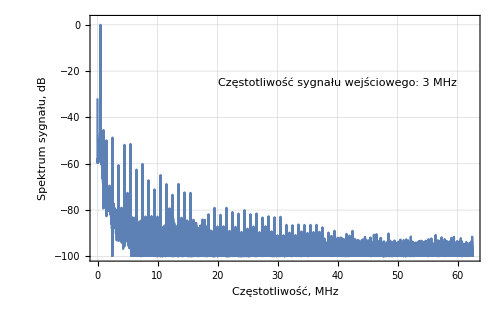

```mathematica
Show[ListPlot[logspectrum,Joined->True,ImageSize->500,PlotRange->{-100,2},DataRange->{0,sfreq/2/1000},Frame->True,GridLines->Automatic,FrameLabel->{"Częstotliwość, MHz","Spektrum sygnału, dB"},Epilog->Inset["Częstotliwość sygnału wejściowego: 3 MHz",{40,-25}]](*,istPlot[{#,logspectrum[[#]]}&/@findpeaks[spectrum,2000],PlotStyle->Orange]*)]
```

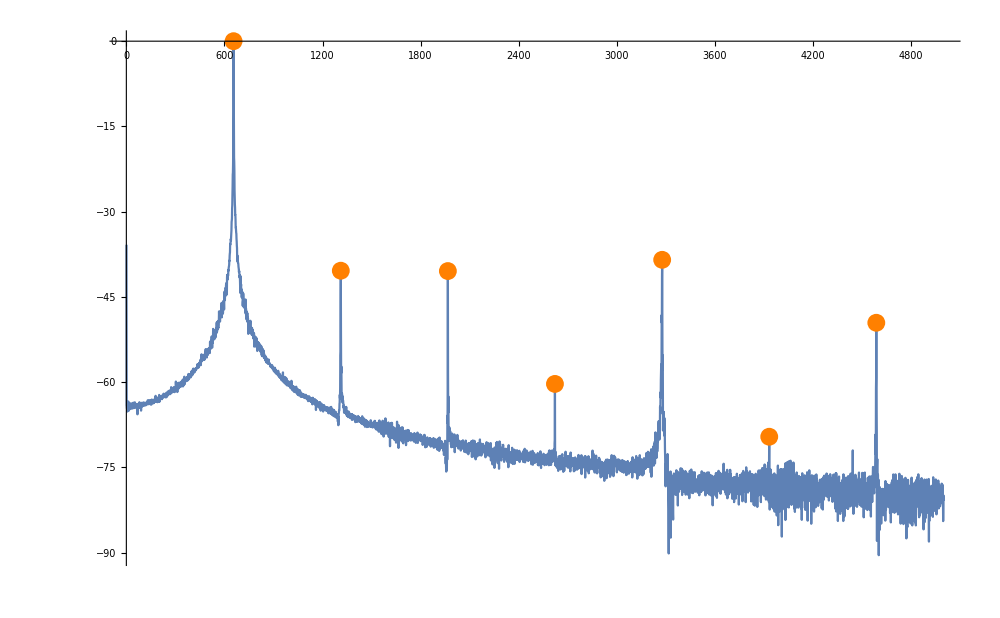
```mathematica
-Graphics-;
```

```mathematica
thd=THD[#1,#2*1000.]&@@@Transpose[{spectrs,freqsMHz}]
```

{0.015366,0.0183905,0.0283996,0.0195085,0.0314973,0.0263193,0.402788,0.0182826}

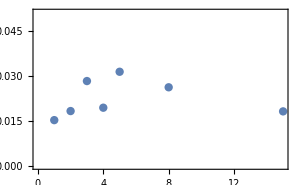

```mathematica
ListPlot[Transpose[{freqsMHz,thd}]]
```

```mathematica
span=20;Manipulate[ListPlot[fourdata[[x;;x+span]],DataRange->{x,x+span},Joined->True,AspectRatio->0.4,ImageSize->1000],{x,1,Length@fourdata-span,10}]
```

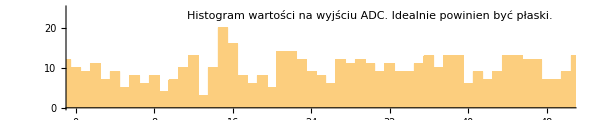

```mathematica
sh=000;Histogram[fourdata,{1},PlotRange->{{0+sh,50+sh},{0,25}},ImageSize->600,AspectRatio->0.2,BaseStyle->{FontSize->14},Epilog->Inset["Histogram wartości na wyjściu ADC. Idealnie powinien być płaski.",{30,23}]]
```

```mathematica
20*Log[10,0.7]
```

-3.09804

```mathematica
10.^(-45/20)
```

0.00562341